```mathematica
A = {{0,0,1,1,0,0,0,0},
                             {0,0,0,1,0,0,0,0},
                  {0,1,1,1,1,1,0,0 },
           {1,0,1,1,1,0,1,1 },
           {0,0,1,1,1,0,1,1 },
            {0,0,0,1,0,0,0,0 },
            {0 ,0,1 ,0 ,1 ,0 ,0 ,0 },
            {0 ,1 ,0 ,0 ,0 ,1 ,0 ,0 }
             }


MatrixForm[A]
```

{{0,0,1,1,0,0,0,0},{0,0,0,1,0,0,0,0},{0,1,1,1,1,1,0,0},{1,0,1,1,1,0,1,1},{0,0,1,1,1,0,1,1},{0,0,0,1,0,0,0,0},{0,0,1,0,1,0,0,0},{0,1,0,0,0,1,0,0}}

(0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
B = {{0	,0	,0	,1	,0	,0	,0	,0	

},
                             {0	,0	,1,	1,	1,	0,	0,	0	

},
                  {0	,0,	0,	1,	0	,0	,0	,0	

},
           {0	,1	,1	,1	,1	,1	,0	,0	

},
           {0	,0	,0	,1	,0	,0	,0	,0	

	},
            {1,	1	,1	,1	,1	,1	,1	,1	

},
            {0	,0	,0	,1	,0	,0	,0	,0	

},
            {	0	,0	,1	,1	,1	,0,0,0

}
             }

MatrixForm[B]
```

{{0,0,0,1,0,0,0,0},{0,0,1,1,1,0,0,0},{0,0,0,1,0,0,0,0},{0,1,1,1,1,1,0,0},{0,0,0,1,0,0,0,0},{1,1,1,1,1,1,1,1},{0,0,0,1,0,0,0,0},{0,0,1,1,1,0,0,0}}

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0)

```mathematica
c = {{1,	1,	1,	1,	0,	0,	0,	0	

},
                             {1	,0	,0	,0	,0	,0	,1	,0	

},
                  {1	,1	,1	,1	,0	,1	,1	,1	

},
           {0	,0	,0	,1	,0	,0	,1	,0	

},
           {1	,1	,1	,1	,0	,0	,0	,0	

},
            {0,0,0,0,0,0,0,0	},
            {0	,0,0	,0	,0,0	,0	,0	},
            {0	,0	,0	,0	,0	,0	,0	,0	}
             }
MatrixForm[c]
```

{{1,1,1,1,0,0,0,0},{1,0,0,0,0,0,1,0},{1,1,1,1,0,1,1,1},{0,0,0,1,0,0,1,0},{1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
N[Eigenvalues[A]]
```

{3.80558,-0.280852+1.1779 ⅈ,-0.280852-1.1779 ⅈ,-0.865229,0.621352,0.,0.,0.}

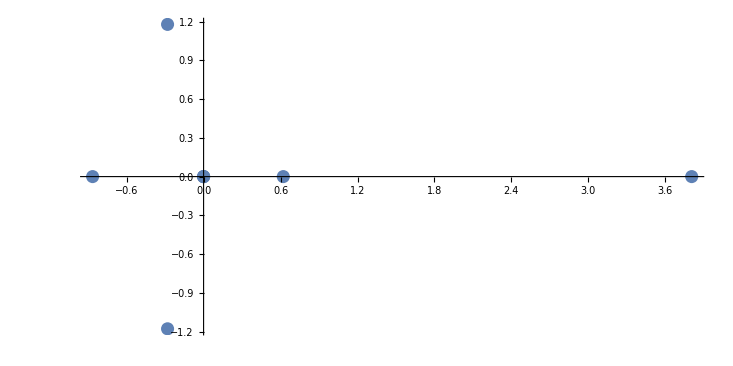

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{3.80558,-0.280852+1.1779 ⅈ,-0.280852-1.1779 ⅈ,-0.865229,0.621352,0.,0.,0.},AspectRatio->0.5, PlotRange -> All]
```

```mathematica
N[Eigenvalues[B]]
```

{3.3781,-0.446909+1.01133 ⅈ,-0.446909-1.01133 ⅈ,-0.484286,0.,0.,0.,0.}

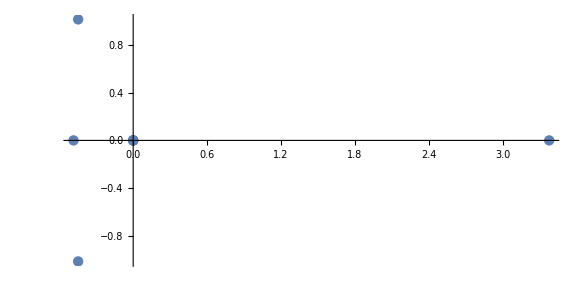

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{3.3781,-0.446909+1.01133 ⅈ,-0.446909-1.01133 ⅈ,-0.484286,0.,0.,0.,0.},AspectRatio->0.5, PlotRange ->All]
```

```mathematica
N[Eigenvalues[c]]
```

{2.41421,1.,-0.414214,0.,0.,0.,0.,0.}

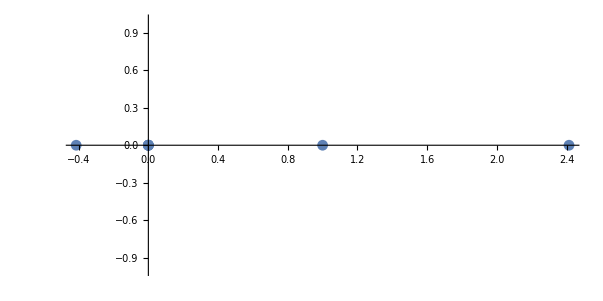

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{2.41421,1.,-0.414214,0.,0.,0.,0.,0.},AspectRatio->0.5, PlotRange ->All]
```